## What’s Here

This notes shows some primary calculations on the propulsion system using only gas.

## Pre

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\Physics\AttackOnTitan

Image size is defined

```mathematica
imgSize=500;
```

## Fundamental Physics & Mathematics

This is something like the Tsiolkovsky rocket equation.

m(d v)/(d t)=-v_e (d m)/(d t)

Next we assume that the velocity of gas in rocket frame v_e is constant.

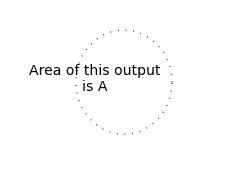

We assume the outlet of the gas is a constant area, and the density of gas at the outlet is ρ (assuming this is constant since we already assumed that the output velocity is constant). Thus we can calculate the mass leakage of the system which works as the propulsion of the equipment.

v-v_0=v_e Log[(ρ v_e A t_0-m_0)/(ρ v_e A t-m_0)]

It is good to make v_0=0, t_0=0.

v=v_e Log[m_0/(-ρ v_e A t+m_0)]

Acceleration

D[v_e Log[m_0/(-ρ v_e A t+m_0)],t]

(A ρ v_e^2)/(m_0-A t ρ v_e)

#### More Real

Now we have to determine the velocity of the gas output. A function gives us the result, that is leakage current of gas is

Q=μ A √((2Δ P)/ρ)

Here we can choose μ∈[0.60,0.62]

Q is just the product of A and v_e, Q=v_e A, i.e.,

v_e=μ √((2 Δ P)/ρ)

Substitution,

v=μ √((2(P-P_0))/(P/P_0 ρ_0))Log[m_0/(m_0-P/P_0 ρ_0 A μ √((2(P-P_0))/(P/P_0 ρ_0))t)]

ve Log[m0/(m0-ρ ve A t)]/.{ve→√2 μ √((P-P0)/(P/P0 ρ0)) ,ρ→(P ρ0)/P0}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Before we use this expression, we need to split the m0 into two parts, one is the mass of gas, the other part is the mass of the body, volume, everything else.

m0 -> M0+m0

result is

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]/.{m0→(M0+m0)}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[(m0+M0)/(m0+M0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Acceleration

D[√2 μ Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),t]

(2 A (P-P0) μ^2)/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)

### Air Drag

(*Parasitic air drag can be decomposed into three parts,*)

Just the simplest case,

-f(v)=m dv/dt-v_e^2 ρ A

dm=-v_e ρ A dt

m=m_0-ρ v_e A t

Case 1

f=-k1 v

In this case

v=1/k1( ρ v_e^2 A - (m_0 - ρ v_e A t)^(k1/(ρ v_e A)) )

Case 2

-f=1/2 ρ0 v^2 C_D Ab

Finally we have the differential equation

dv/(-1/2 ρ_0 C_D A_0 v^2+v_e^2 ρ A)=dt/(m_0-ρ v_e A t)

dv/(A ρ v_e^2-1/2 v^2 A_0 C_D ρ_0)==dt/(m_0-A t ρ v_e)

```mathematica
Integrate[1/(A ρ ve^2-1/2 v^2 A0 C0 ρ0),v]
Integrate[1/(m0-A t ρ ve),t]
```

(√2 ArcTanh[(√A0 √C0 v √ρ0)/(√2 √A ve √ρ)])/(√A √A0 √C0 ve √ρ √ρ0)

-Log[m0-A t ve ρ]/(A ve ρ)

```mathematica
Solve[Integrate[1/(A ρ ve^2-1/2 v^2 A0 C0 ρ0),v]==Integrate[1/(m0-A t ρ ve),t],v]
v/.%[[1]]/.{ve->√2 μ √((P-P0)/(P/P0 ρ0)) ,ρ->(P ρ0)/P0}
```

{{v→-(√2 √A ve √ρ Tanh[(√A0 √C0 √ρ0 Log[m0-A t ve ρ])/(√2 √A √ρ)])/(√A0 √C0 √ρ0)}}

-(2 √A μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(√2 √A √((P ρ0)/P0))])/(√A0 √C0 √ρ0)

## Analysis

### Part 1 Simple Case

#### Simple Examination

Now we just show the scheme of this result

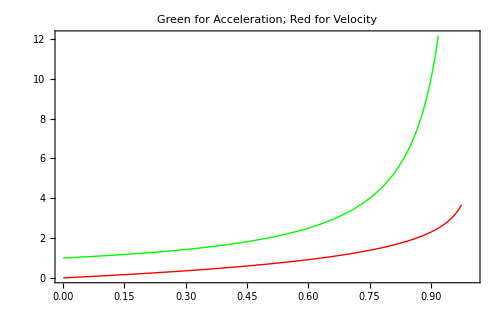

```mathematica
Show[Table[Plot[func[[1]],{t,0,1},PlotStyle->func[[2]],AxesOrigin->{0,0},Frame->True,ImageSize->imgSize],{func,{{1/(1-t),Green},{Log[1/(1-t)],Red}}}],PlotLabel->"Green for Acceleration; Red for Velocity"]
```

#### More Physics

Maybe we want to know the physics of different parameters.

```mathematica
Manipulate[Grid[{{Plot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]},{LogPlot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]}}],{{ve,1,"Velocity of Gas"},1,10,1},{{m0,1,"Initial Mass of Equipment"},1,10,1},{{ρ,1,"Density of Gas at Outlet"},1,50,1},{{A,1,"Area of Outlet"},1,10,1}]
```

#### Even more real

If we put every number in it,

```mathematica
Manipulate[
   "Leakage Constant:"<>ToString[μ]<>";\n"
"Constant Pressure:"<>ToString[P]<>";\n"
"Initial Mass of Gas:"<>ToString[m0]<>";\n"
"Density of Air:"<>ToString[ρ0]<>";\n"
"Area of Outlet:"<>ToString[A]<>";\n"
"Mass of Everything Else:"<>ToString[M0]<>";\n"
Grid[{{Block[{P0=101325},Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]]}}],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Gas"},1,50,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.001,"Area of Outlet"},0.001,1,0.001},{{M0,50,"Mass of Everything Else"},10,100,1}]
```

### Importance of Weight of user

Check the effect of one’s weight, that is M0.

```mathematica
weightList1=Table[Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,A=0.001},
Grid[{{
"Mass of Everything Else:"<>ToString[M0]<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";\n"
},{
Grid[{{Block[{P0=101325},
Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize,PlotRange->{{0,25},{0,400}}]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize,PlotRange->{{0,25},{0,70}}]]}}]}}]],{M0,20,80,10}];
```

```mathematica
ListAnimate[weightList1];
```

```mathematica
weightExp1=Export["Export/weightList1.gif",weightList1,"DisplayDurations"->1.5]
```

Export/weightList1.gif

Calculate the effect of  M0 at 5th second.

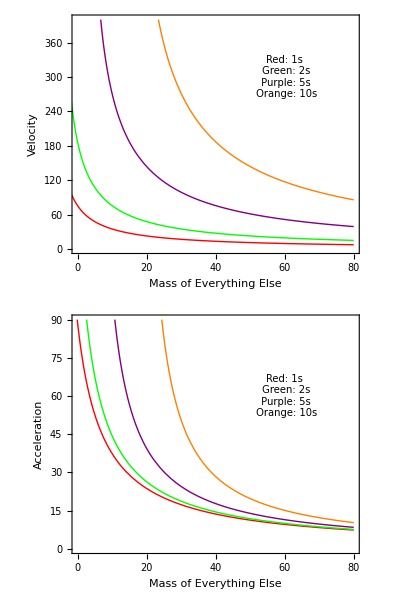
Results at different time t;
Leakage Constant:0.6;Constant Pressure:1000000;Initial Mass of Gas:10;
Density of Air:1.16;Area of Outlet:0.001;

-Graphics-

```mathematica
Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,A=0.001},
Grid[{{
"Results at different time t"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";\n"
},{
Grid[{{
Block[{P0=101325},
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{M0,-m0+(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0,80},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Mass of Everything Else","Velocity"},ImageSize->imgSize,PlotRange->{{0,80},{0,400}}],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,300}]]
]
},{Block[{P0=101325},
Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{M0,-m0+(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0,80},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Mass of Everything Else","Acceleration"},ImageSize->imgSize,PlotRange->{{0,80},{0,90}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,60}]]
]}}]}}]]
```

Pressure analysis

Check pressure of the gas.

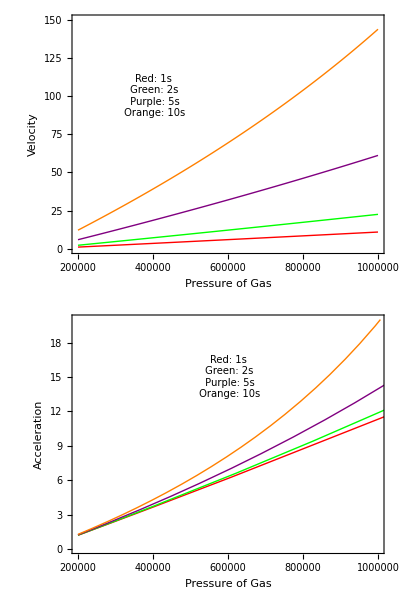
Results at different pressure P;
Leakage Constant:0.6;Constant Pressure:Initial Mass of Gas:10;
Density of Air:1.16;Area of Outlet:0.001;Mass of everything else:50;

-Graphics-

```mathematica
Block[{μ=0.6,M0=50,m0=10,ρ0=1.16,A=0.001,P0=101325},
Grid[{{
"Results at different pressure P"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";"<>"Mass of everything else:"<>ToString[M0]<>";\n"
},{
Grid[{{
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{P,200000,1000000},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Pressure of Gas","Velocity"},ImageSize->imgSize,PlotRange->{Automatic,{0,150}}],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{4*10^5,100}]]
},{Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{P,200000,P/.Solve[M0+m0==(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0][[1]]},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Pressure of Gas","Acceleration"},ImageSize->imgSize,PlotRange->{{200000,1000000},{0,20}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{6*10^5,15}]]
}}]}}]]
```

Size of the outlet

The results for different area of outlet.

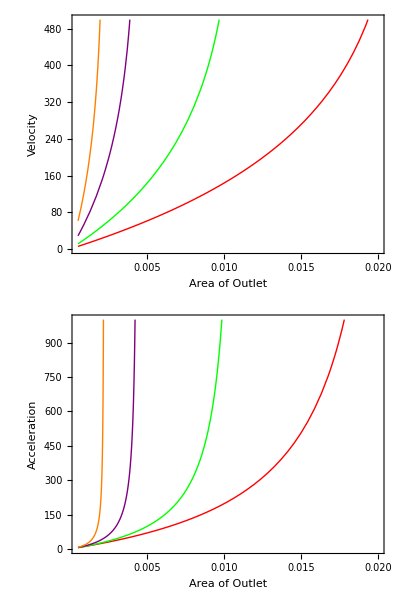
Results at different area of outlet;
Leakage Constant:0.6;Constant Pressure:1000000;Initial Mass of Gas:10;
Density of Air:1.16;Mass of Everything Else:50;

-Graphics-

```mathematica
Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,M0=50,P0=101325},
Grid[{{
"Results at different area of outlet"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Mass of Everything Else:"<>ToString[M0]<>";\n"
},{
Grid[{{
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{A,0.0005,0.02},Frame->True,PlotStyle->t[[2]],PlotRange->{{0.0005,0.02},{0,500}},FrameLabel->{"Area of Outlet","Velocity"},ImageSize->imgSize],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,300}]]
},{
Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{A,0.0005,(M0+m0)/(√2 P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)P0},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Area of Outlet","Acceleration"},ImageSize->imgSize,PlotRange->{{0.0005,0.02},{0,1000}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,60}]]
}}]}}]]
```

### Air Drag

However, the air drag could be quite significant in this case since the velocity is so large.

Before we do the detailed calculation, let’s have a look at the air drag and the propulsion force by airjet.

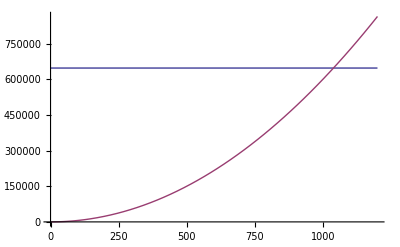

```mathematica
Block[
{P0=101325,M0=50,ρ0=1.2,μ=0.6,m0=10,A=1,A0=1,C0=1,P=1000000},Plot[{A P/P0 ρ0 (√2 μ √((P-P0)/(P/P0 ρ0)))^2,1/2 v^2 A0 C0 ρ0},{v,0,1200}]
]
```

#### Case 1 friction proportional to velocity.

f = k1 v. I don’t know

#### Case 2

v is (2 √A μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(√2 √A √((P ρ0)/P0))])/(√A0 √C0 √ρ0)

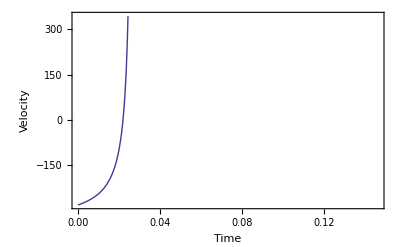

```mathematica
Block[
{P0=101325,M0=50,ρ0=1.2,μ=0.6,m0=10,A=1,A0=1,C0=1,P=200000},
{Plot[-(2 √A μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(√2 √A √((P ρ0)/P0))])/(√A0 √C0 √ρ0),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]
}
]
```

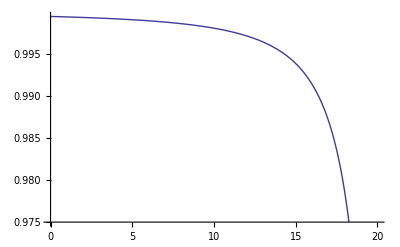

```mathematica
Plot[Tanh[Log[60-2.8t]],{t,0,20}]
```

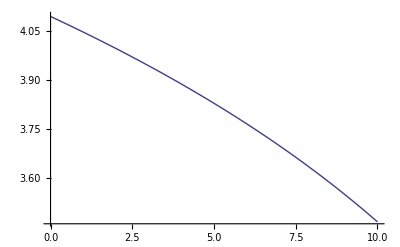

```mathematica
Plot[Log[60-2.8t],{t,0,10}]
```

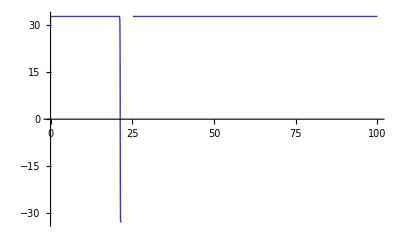

```mathematica
Plot[32.839153460465454 Tanh[7.117759478937173 Log[60-2.7682154945788366 t]],{t,0,100}]
```

```mathematica
Manipulate[
   "Leakage Constant:"<>ToString[μ]<>";\n"
"Constant Pressure:"<>ToString[P]<>";\n"
"Initial Mass of Gas:"<>ToString[m0]<>";\n"
"Density of Air:"<>ToString[ρ0]<>";\n"
"Area of Outlet:"<>ToString[A]<>";\n"
"Mass of Everything Else:"<>ToString[M0]<>";\n"
Grid[{{Block[{P0=101325},Plot[(2 √A μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√A0 √C0 √ρ0 Log[M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(√2 √A √((P ρ0)/P0))])/(√A0 √C0 √ρ0),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]]}}],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Gas"},1,50,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.001,"Area of Outlet"},0.001,1,0.001},{{M0,50,"Mass of Everything Else"},10,100,1},
{{A0,1,"Area of Body"},0.5,2},
{{C0,1,"Drag Coeficient"},0.4,1.2}]
```

## Examples

We take an example here.

Mass of equipment with everything attached including the gas: 10kg

## Draft

```mathematica
Manipulate[Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Equipment"},1,60,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.01,"Area of Outlet"},0.001,1},{{M0,50,"Mass of Everything Else"},10,100,1}]
```